# Tables

```mathematica
Table[n^2,{n,1,5}]
```

{1,4,9,16,25}

```mathematica
Table[2,5]
```

{2,2,2,2,2}

```mathematica
Table[PieChart[{3,4,5}],3]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[a[n],{n,2,7}]
```

{a[2],a[3],a[4],a[5],a[6],a[7]}

```mathematica
f[a_]:=n/2
```

```mathematica
Table[f[n],{n,16}]
```

{1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8}

```mathematica
Table[Range[1,n],{n,1l,5}]
```

Table::iterb: Iterator {n,l,5} does not have appropriate bounds.

```mathematica
Table[Range[1,n],{n,1,5}]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}

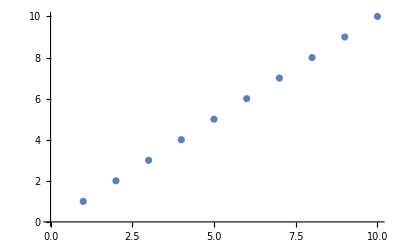
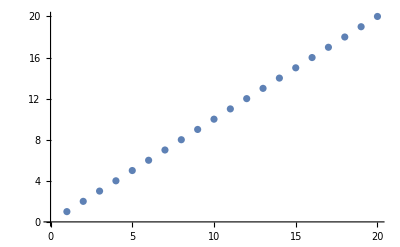
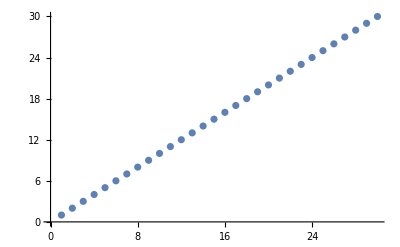

```mathematica
Table[ListPlot[Range[10*n]],{n,3}]
```

```mathematica
Table[Range[10*n],{n,3}]
```

{{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}}

```mathematica
Table[Range[10*n],{n,3}]
```

{{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}}

```mathematica
Table[2^n,{n,1,3}]
```

{2,4,8}

```mathematica
Table[f[n],{n,4,10,2}]
```

{2,3,4,5}

```mathematica
Table[a[n],{n,{1,2,3,4}}]
```

{a[1],a[2],a[3],a[4]}

```mathematica
Table[RandomInteger[10],{20}]
```

{3,10,2,2,10,3,1,5,5,5,0,0,2,8,6,6,3,1,10,3}

```mathematica
Table[x-x^2,{x,0,1,0.1}]
```

{0.,0.09,0.16,0.21,0.24,0.25,0.24,0.21,0.16,0.09,0.}

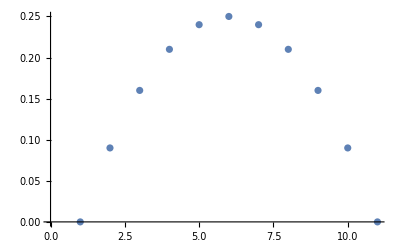

```mathematica
ListPlot[Table[x-x^2,{x,0,1,0.1}]]
```

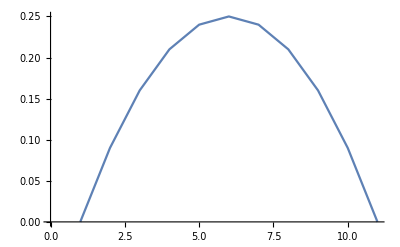

```mathematica
ListLinePlot[Table[x-x^2,{x,0,1,0.1}]]
```

```mathematica
Range[0,1,0.02]-Range[0,1,0.02]^2
```

{0.,0.0196,0.0384,0.0564,0.0736,0.09,0.1056,0.1204,0.1344,0.1476,0.16,0.1716,0.1824,0.1924,0.2016,0.21,0.2176,0.2244,0.2304,0.2356,0.24,0.2436,0.2464,0.2484,0.2496,0.25,0.2496,0.2484,0.2464,0.2436,0.24,0.2356,0.2304,0.2244,0.2176,0.21,0.2016,0.1924,0.1824,0.1716,0.16,0.1476,0.1344,0.1204,0.1056,0.09,0.0736,0.0564,0.0384,0.0196,0.}

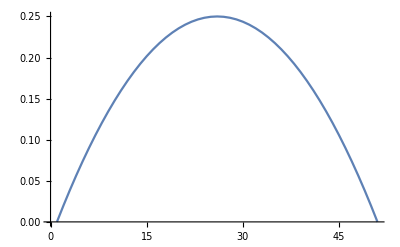

```mathematica
ListLinePlot[Range[0,1,0.02]-Range[0,1,0.02]^2]
```

```mathematica
FactorialZeros[n_Integer]:=Total[Drop[FixedPointList[Floor[#/5]&,n],1]]
```

```mathematica
FactorialZeros[6]
```

1

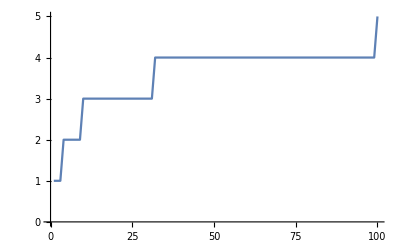

```mathematica
ListLinePlot[Length/@IntegerDigits[Power[Range[100],2]]]
```

```mathematica
First/@IntegerDigits[Power[Range[20],2]]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

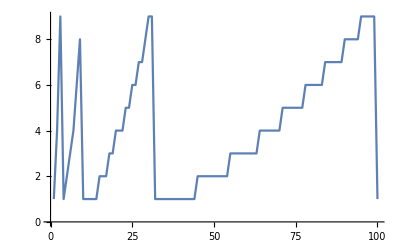

```mathematica
ListLinePlot[First/@IntegerDigits[Power[Range[100],2]]]
```

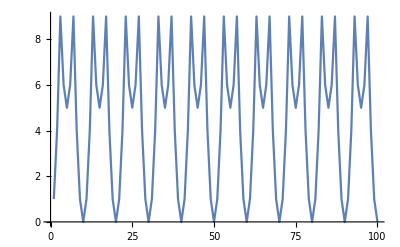

```mathematica
ListLinePlot[Last/@IntegerDigits[ Power[Range[100],2]]]
```

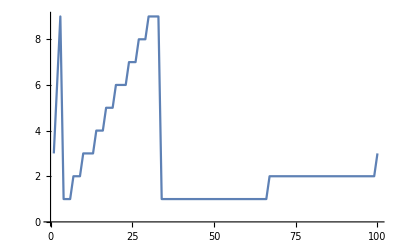

```mathematica
ListLinePlot[First/@IntegerDigits[Table[n*3,{n,1,100}]]]
```

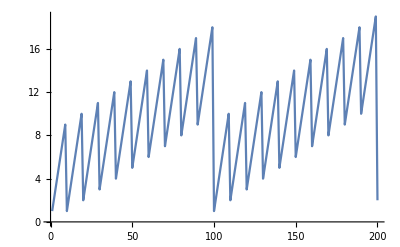

```mathematica
ListLinePlot[Total/@IntegerDigits[Table[n,{n,1,200}]]]
```

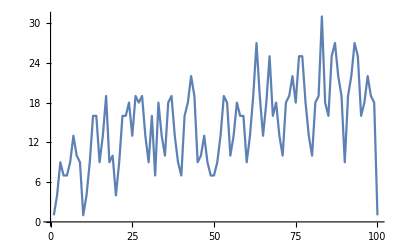

```mathematica
ListLinePlot[Total/@IntegerDigits[Table[n^2,{n,1,100}]]]
```